# Gradients of Scalar Fields

There are conventional coordinate names and orders:  
	x and y are conventional names for Cartesian coordinates
	r and θ are conventional names for polar coordinates
With this convention the two functions below represent the same scalar field!

```mathematica
ϕc[{x_,y_}]:= -(x^2+y^2)
ϕp[{r_,θ_}]:= -r^2
TabView[{
ParametricPlot3D[{x,y,ϕc[{x,y}]},{x,-1,1},{y,-1,0},PlotRange->{All,All,{-1,0}}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],ϕp[{r,θ}]},{r,0,1},{θ,-π,0},PlotRange->{All,All,{-1,0}}]
}]
```

12

The gradient of a scalar field should give the slopes of the tangent plane. The gradient of a scalar field is a vector. The recipe for the gradient of a field in Cartesian coordinates is familiar as is the recipe for a tangent plane!

```mathematica
Gradϕc[{x_,y_}]={D[ϕc[{x,y}],x], D[ϕc[{x,y}],y]};
TPc[{x0_,y0_}][{x_,y_}]=ϕc[{x0,y0}]+Gradϕc[{x0,y0}].{x-x0,y-y0};
{x0,y0}={0.2,-0.3};
ϵ=0.2;
Show[
ParametricPlot3D[{x,y,ϕc[{x,y}]},{x,-1,1},{y,-1,0},PlotRange->{All,All,{-1,0}}],
Plot3D[TPc[{x0,y0}][{x,y}],{x,x0-ϵ,x0+ϵ},{y,y0-ϵ,y0+ϵ},PlotStyle->Blue],
Graphics3D[{Red,PointSize[0.02],Point[{x0,y0,ϕc[{x0,y0}]}]}]
]
```

-Graphics3D-

It is not as easy to do this entirely in polar coordinates.  Mathematica knows the conventional names and the formulas.  You are going to learn how to compute and interpret the second expression.

```mathematica
Grad[ϕc[{x,y}],{x,y}]
Grad[ϕp[{r,θ}],{r,θ}]
```

{-2 x,-2 y}

{-2 r,0}

Here are those two formulas (and one other) as you would see them on a Wikipedia page or book.  You are going to learn how all the formulas (including the fancy ones) are computed.

```mathematica
Grad[f[x,y],{x,y},"Cartesian"]
Grad[f[r,θ],{r,θ},"Polar"]
Grad[f[b1,b2],{b1,b2},"Bipolar"]
```

{f^(1,0)[x,y],f^(0,1)[x,y]}

{f^(1,0)[r,θ],(f^(0,1)[r,θ])/r}

{((-Cos[b1]+Cosh[b2]) f^(1,0)[b1,b2])/a,((-Cos[b1]+Cosh[b2]) f^(0,1)[b1,b2])/a}

You learned one integration theorem about gradients and line integrals in Calculus.  
	https://en.wikipedia.org/wiki/Gradient_theorem
It says for a differentiable curve starting at b and going to a  
	∫_γ Gradϕ(p).dp=ϕ(a)-ϕ(b).

# Divergence of Vector Fields

A vector field is a function u:ℝ^n→ℝ^n. A vector field is easy to plot in two dimensions.

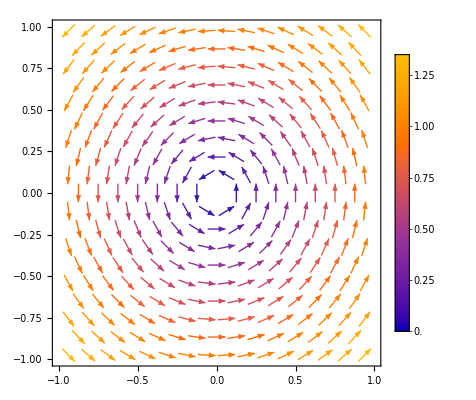

```mathematica
uc[{x_,y_}]:= {-y,x}
VectorPlot[uc[{x,y}],{x,-1,1},{y,-1,1},
PlotLegends->Automatic]
```

You called the gradient of a vector field the Jacobian Matrix in Calculus
	https://en.wikipedia.org/wiki/Jacobian_matrix_and_determinants
It contains all the slopes of all the bits of the function.  You knew the Cartesian recipe and its 3D extension.  You were told the line integral fundamental theorem worked for vector functions!

```mathematica
MatrixForm[Grad[{f1[x,y],f2[x,y]},{x,y},"Cartesian"]]
```

(f1^(1,0)[x,y] | f1^(0,1)[x,y]
f2^(1,0)[x,y] | f2^(0,1)[x,y])

You also had the divergence
	https://en.wikipedia.org/wiki/Divergence
that combined some of the first derivatives in a specific manner to give a scalar field.  You knew the Cartesian recipe and its 3D extension

```mathematica
Div[{f1[x,y],f2[x,y]},{x,y},"Cartesian"]
Div[{f1[x,y,z],f2[x,y,z],f3[x,y,z]},{x,y,z},"Cartesian"]
```

f2^(0,1)[x,y]+f1^(1,0)[x,y]

f3^(0,0,1)[x,y,z]+f2^(0,1,0)[x,y,z]+f1^(1,0,0)[x,y,z]

You probably learned the physical interpretation of  divergence. You probably did not learn how to compute the divergence in other coordinate systems e.g.  polar

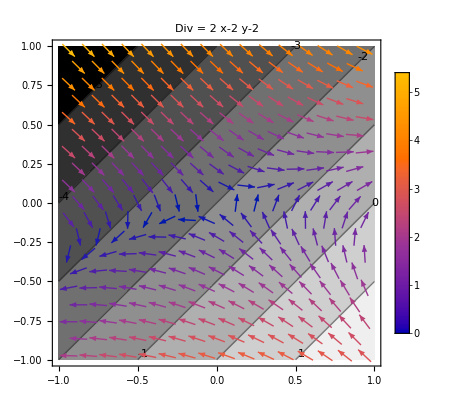

```mathematica
uc[{x_,y_}]:= {x^2+3y,x-2y-y^2}
ucDiv[{x_,y_}]=Div[uc[{x,y}],{x,y},"Cartesian"];
Show[
ContourPlot[ucDiv[{x,y}],{x,-1,1},{y,-1,1},ContourLabels->All,ColorFunction->GrayLevel],
VectorPlot[uc[{x,y}],{x,-1,1},{y,-1,1},
PlotLegends->Automatic],
PlotLabel->StringForm["Div = ``",ucDiv[{x,y}]]
]
```

Naturally Mathematica know the coordinate versions on the Wiki page.  You will learn what the Wiki page means!

```mathematica
Div[{fr[r,θ,z],fθ[r,θ,z],fz[r,θ,z]},{r,θ,z},"Cylindrical"]
```

fz^(0,0,1)[r,θ,z]+(fr[r,θ,z]+fθ^(0,1,0)[r,θ,z])/r+fr^(1,0,0)[r,θ,z]

You learned one integration theorem about divergence and surface integrals in Calculus.   This is the Gauss or divergence theorem
	https://en.wikipedia.org/wiki/Divergence_theorem
It says for a smooth surface S that encloses a volume V
	∫_V Div(u)dV=∫_S u.n dS
where n is the outward unit normal to the surface S=∂V.  You defined the volume integral first and probably wrote 
	dV=dx dy dz
for a little chunk of volume. You worked much harder to define a little patch of surface and the normal n. You probably had two versions one for a function z=f(x,y) and the other for a parameterized surface.  The theorem also works in 2D and 4D etc.

# Curl of Vector Fields

A 3D vector field is a function u:ℝ^3→ℝ^3. A 3D vector field is easy to plot but the plot is hard to read

```mathematica
uc[{x_,y_,z_}]:= {-y,x,x+y}
TabView[Table[
sl->SliceVectorPlot3D[uc[{x,y,z}], sl,{x,-1,1},{y,-1,1},{z,-1,1},PlotLegends->Automatic],
{sl,{"CenterPlanes","BackPlanes","ZStackedPlanes","CenterCutSphere",z==x^2+y^2}}
]]
```

12345

You learnt about the curl in ℝ^3 (and possibly a special ℝ^2 variant) an integration theorem 
	https://en.wikipedia.org/wiki/Stokes%27_theorem	
relating an integral of the Curl over a patch of a surface S and a line integral round the boundary ∂S.   Stokes theorem says 
	∫_S Curl(u).n dS=∫_(∂S) u.τ dl
where n is a normal to the surface patch and τ is the tangent to the boundary curve ∂S.  You need to be careful about how to orient the normal and the boundary curve. You probably only had a computable definition of dS the surface area element for special surfaces. You probably only had a computable definition of the curve length element for special boundary curves.   The special 2D version of this theorem is Green’s Theorem in the plane
	https://en.wikipedia.org/wiki/Green%27s_theorem
which says 
	∫_D (∂_x M-∂_y L)dx dy=∫_(∂D) (L dx + M dy)	
where D is a simple region in ℝ^2.

```mathematica
Curl[{L[x,y],M[x,y],0},{x,y,z},"Cartesian"]
{L[x,y],M[x,y],0}.{dx,dy,0}
```

{0,0,-L^(0,1)[x,y]+M^(1,0)[x,y]}

dx L[x,y]+dy M[x,y]